```mathematica
datapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Single_Board_2_221021\\";
importdata = Import[#,"Table"]&/@(FileNames[datapath<>"\\*.txt"]);

datapathDirect = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Single_Board_2_Direct_Measurement_221026\\";
importdataDirect = Import[#,"Table"]&/@(FileNames[datapathDirect<>"\\*.txt"]);

datapathStack = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\P1 Board Measurements\\";
datapathStackFolders = FileNames["*",datapathStack];
importdataStack = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",datapathStackFolders[[board]]]),{board,1,Dimensions[datapathStackFolders][[1]]}];

backupDatapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Single_Board_2_Repaired_Measurements_230111\\";
backupImportdata = Import[#,"Table"]&/@(FileNames[backupDatapath<>"*.txt"]);

simulationDatapath ="C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\LTSpice\\Data\\Same inputs\\Hand_Measurement_Comparison\\";
simulationImportdata =Import[#,"Table"]&/@(FileNames[simulationDatapath<>"*.txt"]);

multiplexerDatapath ="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\singling_out_device_parts\\obc_single_layer_2022_09_13\\Layer_01\\";
multiplexerImportdata = Import[#,"Table",HeaderLines->2]&/@(FileNames[multiplexerDatapath<>"2D_*.dat"]);

byHandDatapath="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\singling_out_device_parts\\comparison_multiplexer_no_multiplexer\\byHand\\";
byHandImportdata=Import[#,"Table",HeaderLines->2]&/@(FileNames[byHandDatapath<>"2D_*.dat"]);
```

## Data Evaluation of Single Layer Hand Measurements

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];

shuntR = 10.853;
```

```mathematica
(*Sorts imported data into the format: {Board,j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataImportOrdered = Table[importdata[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importdata][[1]]},{entry,1,4}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOrdered = Table[Transpose[{voltageDataImportOrdered[[j,1,;;,1]]*1000,voltageDataImportOrdered[[j,1,;;,2]],voltageDataImportOrdered[[j,3,;;,2]]}],{j,1,Dimensions[importdata][[1]]}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOrdered = Table[Transpose[{voltageDataImportOrdered[[j,1,;;,1]]*1000,voltageDataImportOrdered[[j,2,;;,2]],voltageDataImportOrdered[[j,4,;;,2]]}],{j,1,Dimensions[importdata][[1]]}];

frequencyArray = voltage1JOrdered[[1,;;,1]];

ticks = Table[{(Dimensions[frequencyArray][[1]])/5*i,ToString[i]},{i,1,5}];
ticks23 = Table[{(Dimensions[frequencyArray[[400;;600]]][[1]])/4*(i-1),ToString[i*0.25 +1.75]},{i,1,5}];

ohmTicks = {{500,"500"},{1000,"1000"},{1500,"1500"}};
ohmTicks23 = {{100,"100"},{250,"250"},{500,"500"}};

degTicks = {{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}};
degTicks23 = {{-π/2,"-90°"},{-π/4,"-45°"},{0,"0°"},{π/4,"45°"},{π/2,"90°"}};
```

```mathematica
currentValues = {(((voltage1JOrdered[[1,466,2]])*Exp[I(voltage1JOrdered[[1,466,3]])*2π/360])-((voltage2JOrdered[[1,466,2]])*Exp[I(voltage2JOrdered[[1,466,3]])*2π/360])),
(((voltage1JOrdered[[2,466,2]])*Exp[I(voltage1JOrdered[[2,466,3]])*2π/360])-((voltage2JOrdered[[2,466,2]])*Exp[I(voltage2JOrdered[[2,466,3]])*2π/360]))}/shuntR
```

{0.00265854+0.000261572 ⅈ,0.00243801+0.000776509 ⅈ}

```mathematica
impedancesJOrdered = Table[{frequencyArray[[freq]],(shuntR*(voltage2JOrdered[[j,freq,2]])*Exp[I(voltage2JOrdered[[j,freq,3]])*2π/360])/(((voltage1JOrdered[[j,freq,2]])*Exp[I(voltage1JOrdered[[j,freq,3]])*2π/360])-((voltage2JOrdered[[j,freq,2]])*Exp[I(voltage2JOrdered[[j,freq,3]])*2π/360]))},{j,1,Dimensions[importdata][[1]]},{freq,1,Length[frequencyArray]}];

ImpedancesArray = Table[impedancesJOrdered[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]]]],{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
absImpedancePlots =Table[ListLinePlot[Abs[ImpedancesArray[[x,y,sub]]],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,{0,1500}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotLegends->{"Amplitude of impedance spectrum measured by Hand"}],{x,1,8},{y,1,8},{sub,1,2}];

argImpedancePlots =Table[ListLinePlot[Transpose[{ImpedancesArray[[x,y,sub,;;,1]],Arg[ImpedancesArray[[x,y,sub,;;,2]]]}],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",Ticks->{Automatic,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Phase [°]"},PlotLegends->{"Phase of impedance spectrum measured by Hand"}],{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
Manipulate[absImpedancePlots[[x,y,sub]],{x,1,8,1},{y,1,8,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
Abs[ImpedancesArray[[1,7;;8,;;]]]//Dimensions
```

{2,2,1000,2}

```mathematica
Manipulate[argImpedancePlots[[x,y,sub]],{x,1,8,1},{y,1,8,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
absImpedancePlots23 =Table[ListLinePlot[Abs[ImpedancesArray[[x,y,sub,400;;600]]],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,{0,1500}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotLegends->{"Amplitude of impedance spectrum measured by Hand"}],{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
Manipulate[absImpedancePlots23[[x,y,sub]],{x,1,8,1},{y,1,8,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
overlayTicks = Table[{10^6*i,ToString[i]},{i,1,5}];

overlayImpedancePlots =Table[ListLinePlot[{Abs[ImpedancesArray[[4,5,sub]]],Abs[ImpedancesArray[[4,6,sub]]],Abs[ImpedancesArray[[4,7,sub]]]},PlotLabel->"Nodes: (4,5),(4,6),(4,7), Sub "<>ToString[If[sub==1,"A","B"]],PlotRange->{{0.9*10^6,3*10^6},{0,2000}},AspectRatio->1/4,ImageSize->Full,Ticks->{overlayTicks,Automatic},AxesLabel->{"Frequency [MHz]","Res. [Ω]"},PlotLegends->{"(4,5)","(4,6)","(4,7)"}],{sub,1,2}];
```

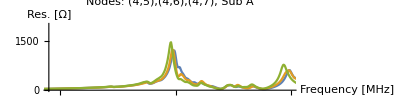

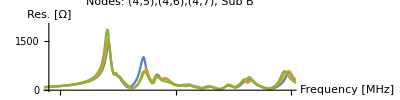

```mathematica
overlayImpedancePlots[[1]]
overlayImpedancePlots[[2]]
```

```mathematica
addedSTDAbs[[1]]
```

0.176437

```mathematica
meanSTDAbs = Table[Around[Mean[Abs[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]],StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];

meanSTDArg = Table[Around[Mean[Arg[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]],StandardDeviation[Arg[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];

meanAbs = Table[Mean[Abs[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];

addedSTDAbs = Table[StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,1,i,2]]]]]+StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,2,i,2]]]]],{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];

meanArg = Table[Mean[Arg[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];

meanSTDAbsPlots = Table[ListLinePlot[meanSTDAbs[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,ohmTicks},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];

meanSTDArgPlots = Table[ListLinePlot[meanSTDArg[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Phases over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,degTicks},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2}];

meanAbs//Dimensions
```

{2,1000}

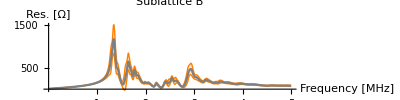

```mathematica
meanSTDAbsPlots[[2]]
```

```mathematica
Manipulate[meanSTDAbsPlots[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[meanSTDArgPlots[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
minAddedSTD23 = Position[addedSTDAbs[[400;;600]],Min[addedSTDAbs[[400;;600]]]][[1,1]];
meanFreqValue23 = frequencyArray[[400;;600]][[minAddedSTD23]];
lineStyle={Thick,Black,Dashed};
line1=Line[{{minAddedSTD23,0},{minAddedSTD23,250}}];
adjustedTicks23= Append[ticks23,{minAddedSTD23,ToString[Round[meanFreqValue23/10^6,0.01]]}];
```

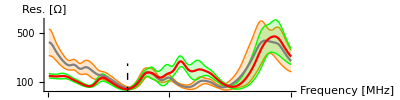

```mathematica
meanSTDAbsPlots23 = ListLinePlot[{meanSTDAbs[[1,400;;600]],meanSTDAbs[[2,400;;600]]},IntervalMarkers->"Bands",PlotStyle->{Gray,Red},IntervalMarkersStyle->{Orange,Green},PlotRange->All,PlotLegends->{"Average Amplitudes and Variances of all A Nodes as a Function of Frequency","Average Amplitudes and Variances of all B Nodes as a Function of Frequency"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{adjustedTicks23,ohmTicks23},AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Epilog->{Directive[lineStyle],line1}]
```

```mathematica
(*Calculates the deviation of the highest peaks of each measured node compared to mean value of peak: {Deviation,{x,y,sub}}*)
cellsHist =Table[{i,i},
{i,8}];

freqRange = 2;
freqLabels = {{1.97,1.69},{2.38,2.38}};

deviationOfNodes = Table[Block[{peakSubABPos = {Position[meanAbs,Max[meanAbs[[1,If[freqs==1,400;;600,466]]]]][[1,2]], Position[meanAbs,Max[meanAbs[[1,If[freqs==1,400;;600,466]]]]][[1,2]]}},(Max[Abs[ImpedancesArray[[x,y,sub,peakSubABPos[[sub]],2]]]]-meanAbs[[sub,peakSubABPos[[sub]]]])/(meanAbs[[sub,peakSubABPos[[sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}]

deviationHist = Table[DiscretePlot3D[Abs[deviationOfNodes[[freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHist,cellsHist,{{0,"0"},{0.2,"20"},{0.4,"40"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis",Rotate["Deviation in %",90 Degree]},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation in % from mean value of sublattice "<>ToString[If[sub==1,A,B]]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{sub,1,2}];
```

{{{{0.167261,0.82887},{0.55343,0.724159},{0.197894,0.700033},{0.159171,0.762287},{0.384226,0.412353},{0.329527,0.785057},{-0.268938,-0.112696},{-0.365851,-0.314386}},{{0.214261,0.14527},{0.145939,-0.0389642},{0.033729,0.164309},{0.0225088,-0.233303},{-0.169186,-0.0140901},{-0.153848,0.077261},{0.421552,0.461669},{0.0375036,0.174809}},{{-0.273473,-0.272658},{-0.215584,-0.204183},{-0.235099,-0.362823},{-0.223654,-0.26707},{-0.166873,-0.212918},{-0.0552395,-0.193374},{0.215916,0.202626},{-0.0931949,-0.161367}},{{-0.314757,-0.330101},{-0.39605,-0.48737},{-0.484014,-0.465605},{-0.362129,-0.46465},{-0.348027,-0.376039},{-0.0834237,-0.0234157},{0.757024,0.330895},{0.403202,0.225229}},{{-0.186566,-0.17059},{-0.311727,-0.0983644},{-0.27228,-0.283546},{-0.260566,-0.203699},{-0.328789,-0.219786},{-0.00232084,0.0404546},{0.34494,0.28239},{0.0722006,0.0263563}},{{-0.27186,-0.149269},{-0.300939,-0.354397},{-0.250197,-0.292249},{-0.637432,-0.421974},{-0.590308,-0.673693},{-0.46585,-0.0310245},{0.410493,0.269094},{0.443786,0.28336}},{{0.0789907,-0.18761},{0.0249748,-0.13017},{-0.0664923,-0.305001},{-0.0201774,-0.334424},{-0.0800251,-0.163885},{0.171742,0.102589},{0.34301,0.299317},{-0.021989,0.0668925}},{{0.425846,0.110206},{0.55493,0.181299},{0.672935,0.0188477},{0.314429,-0.140499},{0.195515,0.0798273},{0.455916,0.549725},{-0.128045,0.146848},{-0.147948,0.24316}}},{{{0.153851,0.356987},{0.0280369,0.211932},{0.00424992,0.103023},{0.0204775,0.123114},{-0.0742195,0.128011},{0.169121,0.342627},{0.431246,0.875699},{0.374171,0.64794}},{{-0.0371275,-0.0206467},{-0.0905995,0.0685713},{0.0226366,-0.00795915},{-0.0363376,0.087607},{0.10991,0.0324362},{-0.0558347,0.209606},{-0.090705,0.154042},{-0.181171,0.0303484}},{{-0.0299792,-0.171682},{-0.125427,-0.183683},{-0.11952,-0.180917},{-0.134405,-0.20399},{-0.114508,-0.203639},{-0.192799,-0.0438608},{-0.221615,-0.10833},{-0.229799,-0.173932}},{{0.104833,-0.105255},{-0.0334549,-0.0169449},{0.300054,-0.0696727},{-0.0020992,-0.119979},{0.0523761,-0.0800854},{-0.175053,-0.118376},{-0.205304,-0.0731913},{-0.276419,-0.144504}},{{-0.124102,-0.147335},{0.160345,-0.107189},{-0.0503571,-0.112295},{0.0566898,-0.100196},{0.0780069,-0.143044},{-0.216593,-0.0875141},{-0.191643,-0.0366717},{-0.223071,-0.096225}},{{0.0501132,-0.163284},{-0.057634,-0.134578},{-0.10318,-0.0441232},{0.962255,-0.134242},{0.0927521,0.816655},{0.776343,-0.113568},{-0.342667,-0.0130467},{-0.168036,-0.175173}},{{-0.0703775,-0.117645},{-0.0128138,-0.134252},{-0.0532093,-0.149375},{-0.104266,-0.0810577},{-0.0546273,-0.138429},{-0.113165,-0.0722852},{-0.0893495,0.0416072},{-0.0584715,-0.127272}},{{0.197743,0.0696672},{-0.0772147,-0.145831},{0.120601,0.0601707},{-0.0331824,-0.176981},{0.0910895,0.00838426},{-0.0192593,0.0713902},{0.292126,0.290224},{-0.0594313,0.0482202}}}}

```mathematica
Manipulate[deviationHist[[freqs,sub]],{freqs,1,2,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
deviationHist[[2,2]]
```

-Graphics3D-

```mathematica
(*Detects minimum and maximum of deviation of the peaks for each sublattice: {min deviation sub A, max deviation sub A, min deviation sub B, max deviation sub B} *)
minMaxDeviationPos = Table[Block[{minmaxDev = MinMax[Flatten[deviationOfNodes[[;;,;;,sub,1]]]]},deviationOfNodes[[Position[deviationOfNodes[[;;,;;,sub,1]],minmaxDev[[extreme]]][[1,1]],
Position[deviationOfNodes[[;;,;;,sub,1]],minmaxDev[[extreme]]][[1,2]],sub
,2]]],{sub,1,2},{extreme,1,2}];

Manipulate[MatrixForm[{"Highest Amplitude Node for Sublattice "<>ToString[If[sub==1,"A","B"]]<>": "<>ToString[minMaxDeviationPos[[sub,1]]],"Lowest Amplitude Node for Sublattice "<>ToString[If[sub==1,"A","B"]]<>": "<>ToString[minMaxDeviationPos[[sub,2]]]<>"}"}],{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
deviationOfNodes[[1,1]]
```

{{0.167261,0.82887},{0.55343,0.724159},{0.197894,0.700033},{0.159171,0.762287},{0.384226,0.412353},{0.329527,0.785057},{-0.268938,-0.112696},{-0.365851,-0.314386}}

```mathematica
sub = 1;
minMaxColor={ToExpression[(Max[Flatten[deviationOfNodes[[;;,;;,sub,1]]]])],ToExpression[(Min[Flatten[deviationOfNodes[[;;,;;,sub,1]]]])]}
BarLegend[{{RGBColor[1,0,0],RGBColor[0,0,0],RGBColor[0,1,0]},{minMaxColor[[2]],minMaxColor[[1]]}}]

Clear[sub]

cells =Table[{i-0.5,i},
{i,8}];
```

{0.425846,-0.314757}

```mathematica
Reverse[Transpose[deviationOfNodes[[2,;;,;;,2]]]]//MatrixForm
```

(0.64794 | 0.0303484 | -0.173932 | -0.144504 | -0.096225 | -0.175173 | -0.127272 | 0.0482202
0.875699 | 0.154042 | -0.10833 | -0.0731913 | -0.0366717 | -0.0130467 | 0.0416072 | 0.290224
0.342627 | 0.209606 | -0.0438608 | -0.118376 | -0.0875141 | -0.113568 | -0.0722852 | 0.0713902
0.128011 | 0.0324362 | -0.203639 | -0.0800854 | -0.143044 | 0.816655 | -0.138429 | 0.00838426
0.123114 | 0.087607 | -0.20399 | -0.119979 | -0.100196 | -0.134242 | -0.0810577 | -0.176981
0.103023 | -0.00795915 | -0.180917 | -0.0696727 | -0.112295 | -0.0441232 | -0.149375 | 0.0601707
0.211932 | 0.0685713 | -0.183683 | -0.0169449 | -0.107189 | -0.134578 | -0.134252 | -0.145831
0.356987 | -0.0206467 | -0.171682 | -0.105255 | -0.147335 | -0.163284 | -0.117645 | 0.0696672)

```mathematica
frequencyArray[[400;;600]]
```

{2.0570575975398242×10^6,2.06195876080528251×10^6,2.06686772048669809×10^6,2.07176796197927615×10^6,2.07667603854133631×10^6,2.0815836833207868×10^6,2.08648406419342791×10^6,2.09139318189954793×10^6,2.09629348114503955×10^6,2.10120171527705679×10^6,2.10610951762646437×10^6,2.11100844398970366×10^6,2.11591536344712995×10^6,2.12082185089457243×10^6,2.12572790678677848×10^6,2.13063353112374898×10^6,2.13553872367810982×10^6,2.14043664914242981×10^6,2.14534325482418353×10^6,2.15024942895070126×10^6,2.15515517106723564×10^6,2.16006048162853403×10^6,2.16496536063459644×10^6,2.16986980785804917×10^6,2.17477382352626591×10^6,2.17967740763924667×10^6,2.1845805604243651×10^6,2.18949044597138709×10^6,2.19439499119289394×10^6,2.19929910463179112×10^6,2.20420278674282599×10^6,2.20910603707125119×10^6,2.21401771204909892×10^6,2.21892011882118822×10^6,2.22382209426541522×10^6,2.22873255211197829×10^6,2.23363368399986939×10^6,2.23853438478727185×10^6,2.2434397142205853×10^6,2.24835074277507374×10^6,2.25325236419848807×10^6,2.25816258762279176×10^6,2.26306336571724387×10^6,2.26796371248383366×10^6,2.27287271923160006×10^6,2.27778133307765529×10^6,2.28268042474155709×10^6,2.28758823413954815×10^6,2.29249517906282563×10^6,2.29739515202709299×10^6,2.30230390411634289×10^6,2.30720303397902217×10^6,2.31211098139283422×10^6,2.31701853613230924×10^6,2.32192569842482044×10^6,2.32682316141108458×10^6,2.3317295194829062×10^6,2.33663548488038987×10^6,2.34154105805828294×10^6,2.34645051841653185×10^6,2.35134799959269003×10^6,2.35625447544407507×10^6,2.36116055884849675×10^6,2.3660662498059537×10^6,2.3709715483164473×10^6,2.37587645437997708×10^6,2.38078096822391672×10^6,2.38568508962089254×10^6,2.39058881879827868×10^6,2.3954982636951172×10^6,2.4004032677567011×10^6,2.40530787937132118×10^6,2.41021209876635112×10^6,2.41511592548704357×10^6,2.42001936021551955×10^6,2.42492240249703173×10^6,2.42982505255895376×10^6,2.43473704836105753×10^6,2.43963893353793537×10^6,2.44454042649522353×10^6,2.44945069903224066×10^6,2.45435342685596015×10^6,2.45925576268746227×10^6,2.46416756340295251×10^6,2.46906913389466354×10^6,2.4739703123941581×10^6,2.47888101375792758×10^6,2.48378142714500427×10^6,2.48869140227725438×10^6,2.49359105100666102×10^6,2.49849969986826181×10^6,2.50340054412845347×10^6,2.50831103062409966×10^6,2.51321110977187345×10^6,2.51812086980862659×10^6,2.52302018407135665×10^6,2.52792921787658997×10^6,2.53282776770902274×10^6,2.53773607551011082×10^6,2.54264402974513359×10^6,2.5475516308688384×10^6,2.55244923096142884×10^6,2.55735803011702956×10^6,2.56226647570656542×10^6,2.56716429862535733×10^6,2.57207201798337337×10^6,2.5769793842300719×10^6,2.58188639691070421×10^6,2.58678271029566531×10^6,2.59168899742689973×10^6,2.59659493121944297×10^6,2.60150051190066733×10^6,2.60640659939781472×10^6,2.61131335764730466×10^6,2.61621976255810296×10^6,2.62112581413020962×10^6,2.62602100815456652×10^6,2.63092633394990116×10^6,2.63583130686129152×10^6,2.64073592643399024×10^6,2.6456507741841051×10^6,2.65055470686093031×10^6,2.65545673846645513×10^6,2.66036180914852594×10^6,2.66526652671927877×10^6,2.67017089095133997×10^6,2.6750749020720832×10^6,2.67997856008150848×10^6,2.68488186520698946×10^6,2.68978481722115248×10^6,2.69469819386358768×10^6,2.6996004592092504×10^6,2.7045023716709693×10^6,2.70941183066497615×10^6,2.71431486044093617×10^6,2.71921753733295191×10^6,2.72411986134102335×10^6,2.72903274844793532×10^6,2.7339343855601328×10^6,2.73883566978838689×10^6,2.74374757532314106×10^6,2.74864817311026854×10^6,2.75354841801345174×10^6,2.75846342174190795×10^6,2.76336476417782251×10^6,2.7682657535024191×10^6,2.77317748327732261×10^6,2.77807778616079304×10^6,2.78297773616031918×10^6,2.78788848436306625×10^6,2.79278774814883945×10^6,2.79769784856398519×10^6,2.80260763497608423×10^6,2.80750587899092352×10^6,2.81241623770256456×10^6,2.81731553923236788×10^6,2.82222577811808151×10^6,2.8271243934341328×10^6,2.83203398430487141×10^6,2.83693191363454389×10^6,2.84184085694505484×10^6,2.84674948602514632×10^6,2.85164639581125812×10^6,2.85655437755849607×10^6,2.86145783320534974×10^6,2.8663668949775456×10^6,2.87127564251932245×10^6,2.87617257026795414×10^6,2.88108067024950333×10^6,2.88598845600063214×10^6,2.89089592774871562×10^6,2.89579150307872624×10^6,2.90069832726658251×10^6,2.90560483767876576×10^6,2.91051103408790368×10^6,2.91541982051057857×10^6,2.92031539402159979×10^6,2.92522231688963075×10^6,2.93012892575461592×10^6,2.93503522038918163×10^6,2.93994120124807523×10^6,2.94484686787654937×10^6,2.94975222072935139×10^6,2.95465725980648131×10^6,2.95956198488056589×10^6,2.96446245624792937×10^6,2.96936820154769521×10^6,2.97427363307178894×10^6,2.97917875082021055×10^6,2.98408355433821271×10^6,2.98898804408054275×10^6,2.993892219819827×10^6,2.99879608178343915×10^6,3.00369962997137964×10^6,3.0086028643836471×10^6,3.01351783718928345×10^6,3.01842257908901956×10^6,3.02332651926917606×10^6,3.02823014544628677×10^6,3.03313345784772582×10^6,3.03803645647349231×10^6}

```mathematica
stdAbs = Table[StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,1,i,2]]]]]+StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,2,i,2]]]]],{i,1,Length[ImpedancesArray[[1,1,1,;;,2]]]}];
```

```mathematica
frequencyArray[[400+Position[stdAbs[[400;;500]],Min[stdAbs[[400;;500]]]][[1,1]]]]/1000
400+Position[stdAbs[[400;;500]],Min[stdAbs[[400;;500]]]][[1,1]]
```

2380.78096822391672

466

## Data Evaluation of Single Component Direct Measurements

```mathematica
(*Sorts imported data into the format: {Board,j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataComponentOrdered = Table[importdataComponent[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importdataComponent][[1]]},{entry,1,4}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOrderedComponent = Table[Transpose[{voltageDataComponentOrdered[[j,1,;;,1]]*1000,voltageDataComponentOrdered[[j,1,;;,2]],voltageDataComponentOrdered[[j,3,;;,2]]}],{j,1,Dimensions[importdataComponent][[1]]}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOrderedComponent = Table[Transpose[{voltageDataComponentOrdered[[j,1,;;,1]]*1000,voltageDataComponentOrdered[[j,2,;;,2]],voltageDataComponentOrdered[[j,4,;;,2]]}],{j,1,Dimensions[importdataComponent][[1]]}];

frequencyArrayComponent = voltage1JOrderedComponent[[1,;;,1]];

componentNames = Table[FileNameTake[FileNames[datapathComponent<>"\\*.txt"][[entry]]],{entry,1,Dimensions[importdataComponent][[1]]}];

numberOfNodes = 3;
numberOfComponents = 7;
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {j,1,{}⟦1⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {j,1,{}⟦1⟧} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {j,1,{}⟦1⟧} does not have appropriate bounds.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {entry,1,{}⟦1⟧} does not have appropriate bounds.

```mathematica
impedancesJOrderedComponent = Table[{frequencyArrayComponent[[freq]],(shuntR*(voltage2JOrderedComponent[[j,freq,2]])*Exp[I(voltage2JOrderedComponent[[j,freq,3]])*2π/360])/(((voltage1JOrderedComponent[[j,freq,2]])*Exp[I(voltage1JOrderedComponent[[j,freq,3]])*2π/360])-((voltage2JOrderedComponent[[j,freq,2]])*Exp[I(voltage2JOrderedComponent[[j,freq,3]])*2π/360]))},{j,1,Dimensions[importdataComponent][[1]]},{freq,1,Length[frequencyArrayComponent]}];
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {j,1,{}⟦1⟧} does not have appropriate bounds.

```mathematica
posToDeviation[posAsString_]:=Block[{positionCoords = If[ToExpression["{"<>StringSplit[StringSplit[StringSplit[posAsString,"_"][[2]],{"(",")"}]][[1]]<>"}"][[3]]==2,Position[deviationOfNodes[[;;,;;,;;,2,1;;2]],ToExpression["{"<>StringSplit[StringSplit[StringSplit[posAsString,"_"][[2]],{"(",")"}]][[1]]<>"}"][[{1,2}]]],Position[deviationOfNodesMulti[[;;,;;,;;,;;,2,1;;3]],ToExpression["{"<>StringSplit[StringSplit[StringSplit[posAsString,"_"][[2]],{"(",")"}]][[1]]<>"}"]]]},{If[Length[positionCoords[[1]]]==3,deviationOfNodes[[positionCoords[[1,1]],positionCoords[[1,2]],positionCoords[[1,3]],1]],deviationOfNodesMulti[[positionCoords[[1,1]],positionCoords[[1,2]],positionCoords[[1,3]],positionCoords[[1,4]],1]]],
If[Length[positionCoords[[1]]]==3,deviationOfNodes[[positionCoords[[2,1]],positionCoords[[2,2]],positionCoords[[2,3]],1]],deviationOfNodesMulti[[positionCoords[[2,1]],positionCoords[[2,2]],positionCoords[[2,3]],positionCoords[[2,4]],1]]]}];
```

```mathematica
absImpedanceComponentPlots =Table[ListLinePlot[{Abs[impedancesJOrderedComponent[[component,400;;600]]],Abs[impedancesJOrderedComponent[[component+1*numberOfComponents,400;;600]]],Abs[impedancesJOrderedComponent[[component+2*numberOfComponents,400;;600]]]},PlotLabel->"Amplitude of Component: "<>ToString[StringSplit[componentNames[[component]],"_"][[3]]],Ticks->{Automatic,ohmTicks},PlotRange->All,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotLegends->{"Node: "<>ToString[StringSplit[componentNames[[component]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component]]]],"Node: "<>ToString[StringSplit[componentNames[[component+1*numberOfComponents]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component+1*numberOfComponents]]]],"Node: "<>ToString[StringSplit[componentNames[[component+2*numberOfComponents]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component+2*numberOfComponents]]]]}],{component,1,numberOfComponents}];

argImpedanceComponentPlots =Table[ListLinePlot[{Transpose[{impedancesJOrderedComponent[[component,;;,1]],Arg[impedancesJOrderedComponent[[component,;;,2]]]}][[400;;600]],Transpose[{impedancesJOrderedComponent[[component+1*numberOfComponents,;;,1]],Arg[impedancesJOrderedComponent[[component+1*numberOfComponents,;;,2]]]}][[400;;600]],Transpose[{impedancesJOrderedComponent[[component+2*numberOfComponents,;;,1]],Arg[impedancesJOrderedComponent[[component+2*numberOfComponents,;;,2]]]}][[400;;600]]},PlotLabel->"Phase of Component: "<>ToString[StringSplit[componentNames[[component]],"_"][[3]]],Ticks->{Automatic,degTicks},PlotRange->All,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Phase [°]"},PlotLegends->{"Node: "<>ToString[StringSplit[componentNames[[component]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component]]]],"Node: "<>ToString[StringSplit[componentNames[[component+1*numberOfComponents]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component+1*numberOfComponents]]]],"Node: "<>ToString[StringSplit[componentNames[[component+2*numberOfComponents]],"_"][[2]]]<>" with Sublattice Deviation in Ω {A,B}: "<>ToString[posToDeviation[componentNames[[component+2*numberOfComponents]]]]}],{component,1,numberOfComponents}];
```

Part::take: Cannot take positions 400 through 600 in {frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[1/360 ⅈ voltage2JOrderedComponent⟦j,freq,3⟧ 2 π])/(voltage1JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ Part[«4»] 2 «2»]-voltage2JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]])}.

Part::partw: Part 8 of Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ voltage2JOrderedComponent⟦j,freq,3⟧ 2 (π Power[«2»])])/(voltage1JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]]-Part[«4»] Exp[«1»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}] does not exist.

Part::partw: Part 15 of Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ voltage2JOrderedComponent⟦j,freq,3⟧ 2 (π Power[«2»])])/(voltage1JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]]-Part[«4»] Exp[«1»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}] does not exist.

StringJoin::string: String expected at position 1 in datapathComponent<>\*.txt.

StringJoin::string: String expected at position 1 in datapathComponent<>\\\*\.txt.

StringJoin::string: String expected at position 1 in datapathComponent<>\*\.txt.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Part::pkspec1: The expression entry cannot be used as a part specification.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[FileNameTake[{}⟦entry⟧],_].

Part::partw: Part 3 of StringSplit[FileNameTake[{}⟦entry⟧],_] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression entry cannot be used as a part specification.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[FileNameTake[{}⟦entry⟧],_].

Part::pkspec1: The expression entry cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[FileNameTake[{}⟦entry⟧],_].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in 0.82887.

General::stop: Further output of Part::take will be suppressed during this calculation.

Table::iterb: Iterator {j,1.,{}⟦1⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 400 through 600 in {{Transpose[1000 Table[importdataComponent⟦j,Span[«2»]⟧,{j,1,Part[«2»]},{entry,1,4}]⟦j,1,1;;All,1⟧],Arg[freq]},{10.853 ⅇ^(1/180 ⅈ π Table[Transpose[«1»],{«3»}]⟦j,freq,3⟧) Table[Transpose[{Times[«2»],Part[«5»],Part[«5»]}],{j,1,{}⟦1⟧}]⟦j,freq,2⟧,Arg[1/(ⅇ^Times[«3»] Table[«2»]⟦j,freq,2⟧-ⅇ^Times[«3»] Table[«2»]⟦j,freq,2⟧)]}}.

Part::partw: Part 8 of Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ voltage2JOrderedComponent⟦j,freq,3⟧ 2 (π Power[«2»])])/(voltage1JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]]-Part[«4»] Exp[«1»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}] does not exist.

Part::take: Cannot take positions 400 through 600 in {Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]])/(Times[«2»]+Times[«2»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦8,1;;All,1⟧,Arg[Table[{frequencyArrayComponent⟦freq⟧,(shuntR Part[«4»] Exp[«1»])/Plus[«2»]},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦8,1;;All,2⟧]}.

Part::partw: Part 15 of Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ voltage2JOrderedComponent⟦j,freq,3⟧ 2 (π Power[«2»])])/(voltage1JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]]-Part[«4»] Exp[«1»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 400 through 600 in {Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[Times[«4»]])/(Times[«2»]+Times[«2»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦15,1;;All,1⟧,Arg[Table[{frequencyArrayComponent⟦freq⟧,(shuntR Part[«4»] Exp[«1»])/Plus[«2»]},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦15,1;;All,2⟧]}.

General::stop: Further output of Part::take will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in datapathComponent<>\\\*\.txt.

StringJoin::string: String expected at position 1 in datapathComponent<>\*\.txt.

StringJoin::string: String expected at position 1 in datapathComponent<>\\\*\.txt.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[FileNameTake[{}⟦entry⟧],_].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Table::iterb: Iterator {j,1.,{}⟦1⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ Part[«4»] 2 «2»])/(Part[«4»] Exp[«1»]-Times[«2»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦2,1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[ⅈ Part[«4»] 2 «2»])/(Part[«4»] Exp[«1»]-Times[«2»])},{j,1,{}⟦1⟧},{freq,1,Length[frequencyArrayComponent]}]⟦2,1;;All,2⟧ is longer than depth of object.

Part::partd: Part specification Table[{frequencyArrayComponent⟦freq⟧,(shuntR voltage2JOrderedComponent⟦j,freq,2⟧ Exp[0.0174532925199433 ⅈ Part[«4»]])/(Power[«2»] Part[«4»]-1. Power[«2»] Part[«4»])},{j,1.,{}⟦1⟧},{freq,1.,Length[frequencyArrayComponent]}]⟦2,1;;All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
meanAbs[[;;,;;10]]
```

{{4.14296,4.32129,4.50178,4.68186,4.86165,5.04152,5.22318,5.40675,5.59141,5.77545},{8.4117,8.78871,9.16824,9.55308,9.9326,10.3109,10.6927,11.073,11.4535,11.8404}}

```mathematica
Manipulate[Grid[{{absImpedanceComponentPlots[[component]]},{argImpedanceComponentPlots[[component]]}}],{component,1,numberOfComponents,1},SaveDefinitions->True];
```

```mathematica
Manipulate[argImpedanceComponentPlots[[component]],{component,1,numberOfComponents,1},SaveDefinitions->True];
```

## Data Evaluation of Multiple Layer Hand Measurements

```mathematica
(*Sorts imported data into the format: {Board, j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataMultiOrdered = Table[importdataStack[[board,j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{board,1,Dimensions[importdataStack][[1]]},{j,1,Dimensions[importdataStack][[2]]},{entry,1,4}];
(*Sorts imported data into the format: {Board, j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOrderedMulti = Table[Transpose[{voltageDataMultiOrdered[[board,j,1,;;,1]]*1000,voltageDataMultiOrdered[[board,j,1,;;,2]],voltageDataMultiOrdered[[board,j,3,;;,2]]}],{board,1,Dimensions[importdataStack][[1]]},{j,1,Dimensions[importdataStack][[2]]}];
(*Sorts imported data into the format: {Board, j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOrderedMulti = Table[Transpose[{voltageDataMultiOrdered[[board,j,1,;;,1]]*1000,voltageDataMultiOrdered[[board,j,2,;;,2]],voltageDataMultiOrdered[[board,j,4,;;,2]]}],{board,1,Dimensions[importdataStack][[1]]},{j,1,Dimensions[importdataStack][[2]]}];

frequencyArrayMulti = voltage1JOrderedMulti[[1,1,;;,1]];

ticks = Table[{(Dimensions[frequencyArrayMulti][[1]])/5*i,ToString[i]},{i,1,5}];
```

```mathematica
subsystemMulti = Dimensions[importdataStack][[2]];

xMinMaxMulti =MinMax[correspondingNodeCoords[[;;subsystemMulti,1]]];
yMinMaxMulti =MinMax[correspondingNodeCoords[[;;subsystemMulti,2]]];

impedancesJOrderedMulti = Table[{frequencyArrayMulti[[freq]],(shuntR*(voltage2JOrderedMulti[[board,j,freq,2]])*Exp[I(voltage2JOrderedMulti[[board,j,freq,3]])*2π/360])/(((voltage1JOrderedMulti[[board,j,freq,2]])*Exp[I(voltage1JOrderedMulti[[board,j,freq,3]])*2π/360])-((voltage2JOrderedMulti[[board,j,freq,2]])*Exp[I(voltage2JOrderedMulti[[board,j,freq,3]])*2π/360]))},{board,1,Dimensions[importdataStack][[1]]},{j,1,Dimensions[importdataStack][[2]]},{freq,1,Length[frequencyArrayMulti]}];

ImpedancesArrayMulti = Table[impedancesJOrderedMulti[[board,Position[p1,{x,y,sub}][[1,1]]]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]]},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]]},{board,1,Dimensions[importdataStack][[1]]},{sub,1,2}];
```

```mathematica
ImpedancesArrayMulti//Dimensions
```

{4,4,4,2,1000,2}

```mathematica
absImpedancePlotsMulti =Table[ListLinePlot[Abs[ImpedancesArrayMulti[[x,y,board,sub]]],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[board]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,{0,1500}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotStyle->Orange,PlotLegends->{"Amplitude of impedance spectrum of multiple layers measured by Hand"}],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]]},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]]},{board,1,Dimensions[importdataStack][[1]]},{sub,1,2}];

argImpedancePlotsMulti =Table[ListLinePlot[Transpose[{ImpedancesArrayMulti[[x,y,board,sub,;;,1]],Arg[ImpedancesArrayMulti[[x,y,board,sub,;;,2]]]}],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[board]<>","<>ToString[If[sub==1,"A","B"]]<>")",Ticks->{Automatic,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},PlotRange->{Automatic,All},PlotStyle->Orange,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Phase [°]"},PlotLegends->{"Phase of impedance spectrum of multiple layers measured by Hand"}],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]]},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]]},{board,1,Dimensions[importdataStack][[1]]},{sub,1,2}];
```

```mathematica
Manipulate[absImpedancePlotsMulti[[x,y,board,sub]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]],1},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]],1},{board,1,Dimensions[importdataStack][[1]],1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
Manipulate[argImpedancePlotsMulti[[x,y,board,sub]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]],1},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]],1},{board,1,Dimensions[importdataStack][[1]],1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
Manipulate[Show[absImpedancePlots[[x,y,sub]],absImpedancePlotsMulti[[x,y,layer,sub]]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]],1},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]],1},{sub,1,2,1},{layer,1,Dimensions[importdataStack][[1]],1},SaveDefinitions->True]
```

```mathematica
Manipulate[Show[argImpedancePlots[[x,y,sub]],argImpedancePlotsMulti[[x,y,layer,sub]]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]],1},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]],1},{sub,1,2,1},{layer,1,Dimensions[importdataStack][[1]],1},SaveDefinitions->True]
```

```mathematica
meanSTDAbsMulti = Table[Around[Mean[Abs[Flatten[ImpedancesArrayMulti[[;;,;;,;;,sub,i,2]]]]],StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayMulti[[1,1,1,1,;;,2]]]}];

meanSTDArgMulti = Table[Around[Mean[Arg[Flatten[ImpedancesArrayMulti[[;;,;;,;;,sub,i,2]]]]],StandardDeviation[Arg[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayMulti[[1,1,1,1,;;,2]]]}];

meanAbsMulti = Table[Mean[Abs[Flatten[ImpedancesArrayMulti[[;;,;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayMulti[[1,1,1,1,;;,2]]]}];

meanArgMulti = Table[Mean[Arg[Flatten[ImpedancesArrayMulti[[;;,;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayMulti[[1,1,1,1,;;,2]]]}];
```

```mathematica
meanSTDAbsPlotsMulti = Table[ListLinePlot[meanSTDAbsMulti[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes in P1 of Boards 1-4"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,ohmTicks},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];

meanSTDArgPlotsMulti = Table[ListLinePlot[meanSTDArg[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Gray,IntervalMarkersStyle->Orange,PlotRange->All,PlotLegends->{"Average Phases over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes in P1 of Boards 1-4"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,degTicks},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2}];
```

```mathematica
Manipulate[meanSTDAbsPlotsMulti[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[meanSTDArgPlotsMulti[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
deviationOfNodes = Table[Block[{peakSubABPos = {Position[meanAbs,Max[meanAbs[[1,If[freqs==1,400;;600,466]]]]][[1,2]], Position[meanAbs,Max[meanAbs[[1,If[freqs==1,400;;600,466]]]]][[1,2]]}},(Max[Abs[ImpedancesArray[[x,y,sub,peakSubABPos[[sub]],2]]]]-meanAbs[[sub,peakSubABPos[[sub]]]])/(meanAbs[[sub,peakSubABPos[[sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
cellsHistMulti =Table[{i,i},
{i,xMinMaxMulti[[2]]}];

(*Calculates the deviation of the highest peaks of each measured node compared to mean value of peak: {Deviation,{x,y,z,sub}}*)
deviationOfNodesMulti = Table[Block[{peakSubABPos = {Position[meanAbsMulti,Max[meanAbsMulti[[1,If[freqs==1,400;;600,466]]]]][[1,2]], Position[meanAbsMulti,Max[meanAbsMulti[[1,If[freqs==1,400;;600,466]]]]][[1,2]]}},(Max[Abs[ImpedancesArrayMulti[[x,y,board,sub,peakSubABPos[[sub]],2]]]]-meanAbsMulti[[sub,peakSubABPos[[sub]]]])/(meanAbsMulti[[sub,peakSubABPos[[sub]]]])],{freqs,1,2},{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]]},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]]},{board,1,Dimensions[importdataStack][[1]]},{sub,1,2}];

deviationHistMulti = Table[DiscretePlot3D[Abs[deviationOfNodesMulti[[freqs,x,y,board,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{0.3,"0.2"},{0.5,"0.4"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation in % from mean value of sublattice "<>ToString[If[sub==1,A,B]]<>" of board "<>ToString[board]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{board,1,4},{sub,1,2}];
```

```mathematica
Manipulate[deviationHistMulti[[freqs,board,sub]],{freqs,1,2,1},{board,1,4,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
(*Detects minimum and maximum of deviation of the peaks for each sublattice: {min deviation sub A, max deviation sub A, min deviation sub B, max deviation sub B} *)
minMaxDeviationPosMulti = Table[Block[{minmaxDev = MinMax[Flatten[deviationOfNodesMulti[[;;,;;,;;,sub,1]]]]},deviationOfNodesMulti[[Position[deviationOfNodesMulti[[;;,;;,;;,sub,1]],minmaxDev[[extreme]]][[1,1]],
Position[deviationOfNodesMulti[[;;,;;,;;,sub,1]],minmaxDev[[extreme]]][[1,2]],Position[deviationOfNodesMulti[[;;,;;,;;,sub,1]],minmaxDev[[extreme]]][[1,3]],sub
,2]]],{sub,1,2},{extreme,1,2}];

Manipulate[MatrixForm[{"Highest Amplitude Node for Sublattice "<>ToString[If[sub==1,"A","B"]]<>": "<>ToString[minMaxDeviationPosMulti[[sub,1]]],"Lowest Amplitude Node for Sublattice "<>ToString[If[sub==1,"A","B"]]<>": "<>ToString[minMaxDeviationPosMulti[[sub,2]]]<>"}"}],{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
maxPosMulti ={Position[meanAbsMulti,Max[meanAbsMulti[[1,350;;450]]]][[1]], Position[meanAbsMulti,Max[meanAbsMulti[[1,225;;325]]]][[1]]};
usedFreqMulti = {frequencyArrayMulti[[maxPosMulti[[1,2]]]] ,frequencyArrayMulti[[maxPosMulti[[2,2]]]]}
maxPosMulti//MatrixForm
```

{1.97367631699307822×10^6,1.68918918916460825×10^6}

(1 | 383
1 | 325)

```mathematica
cellsQuadrant =Table[{i-0.5,i},
{i,xMinMaxMulti[[2]]}];



(*Calculates the deviation of the highest peaks of each measured node compared to mean value of peak: {Deviation,{x,y,sub}}*)
colorDeviationOfNodesMulti =Block[{peakSubABPos = {Position[meanAbsMulti,Max[meanAbsMulti[[1,350;;450]]]][[1]], Position[meanAbsMulti,Max[meanAbsMulti[[1,225;;325]]]][[1]]}},Table[If[deviationOfNodesMulti[[x,y,board,sub,1]]>0,RGBColor[(deviationOfNodesMulti[[x,y,board,sub,1]])/(Max[Flatten[deviationOfNodesMulti[[;;,;;,;;,sub,1]]]]),0,0],RGBColor[0,(deviationOfNodesMulti[[x,y,board,sub,1]])/(Min[Flatten[deviationOfNodesMulti[[;;,;;,;;,sub,1]]]]),0]],{x,xMinMaxMulti[[1]],xMinMaxMulti[[2]]},{y,yMinMaxMulti[[1]],yMinMaxMulti[[2]]},{board,1,Dimensions[importdataStack][[1]]},{sub,1,2}]];
```

Part::partw: Part 3 of {{«1»},{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Manipulate[Grid[{{ArrayPlot[Reverse[Transpose[colorDeviationOfNodesMulti[[;;,;;,z,sub]]]],Axes->True,AxesLabel->{"x-Axis","y-Axis"},Mesh->{xMinMaxMulti[[2]]-1,yMinMaxMulti[[2]]-1},MeshStyle-> Black,AspectRatio->1,Frame->False,Ticks->{cellsQuadrant,cellsQuadrant},ImageSize->Medium,PlotLegends->Automatic]},{BarLegend[{{RGBColor[0,1,0],RGBColor[0,0,0],RGBColor[1,0,0]},{(Min[Flatten[deviationOfNodesMulti[[;;,;;,;;,sub,1]]]]),(Max[Flatten[deviationOfNodesMulti[[;;,;;,;;,sub,1]]]])}},LegendLayout->"Row",LegendLabel->"Deviation from mean in Ω of sublattice "<>ToString[If[sub==1,A,B]]<>" of board "<>ToString[z]]
}}],{z,1,Dimensions[importdataStack][[1]],1},{sub,1,2,1},SaveDefinitions->True]
```

## Data Evaluation of Direct Layer Hand Measurements

```mathematica
(*Sorts imported data into the format: {Board, j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataDirectOrdered = Table[importdataDirect[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importdataDirect][[1]]},{entry,1,4}];
(*Sorts imported data into the format: {Board, j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOrderedDirect = Table[Transpose[{voltageDataDirectOrdered[[j,1,;;,1]]*1000,voltageDataDirectOrdered[[j,1,;;,2]],voltageDataDirectOrdered[[j,3,;;,2]]}],{j,1,Dimensions[importdataDirect][[1]]}];
(*Sorts imported data into the format: {Board, j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOrderedDirect = Table[Transpose[{voltageDataDirectOrdered[[j,1,;;,1]]*1000,voltageDataDirectOrdered[[j,2,;;,2]],voltageDataDirectOrdered[[j,4,;;,2]]}],{j,1,Dimensions[importdataDirect][[1]]}];

frequencyArrayDirect = voltage1JOrderedDirect[[1,;;,1]];

ticks = Table[{(Dimensions[frequencyArrayDirect][[1]])/5*i,ToString[i]},{i,1,5}];
```

```mathematica
p1Direct//Dimensions
```

{}

```mathematica
p1Direct=Flatten[Table[{5-p,5-q,2},{p,1,4},{q,1,4}],1];

xMinMaxDirect =MinMax[p1Direct[[;;,1]]];
yMinMaxDirect =MinMax[p1Direct[[;;,2]]];

impedancesJOrderedDirect = Table[{frequencyArrayDirect[[freq]],(shuntR*(voltage2JOrderedDirect[[j,freq,2]])*Exp[I(voltage2JOrderedDirect[[j,freq,3]])*2π/360])/(((voltage1JOrderedDirect[[j,freq,2]])*Exp[I(voltage1JOrderedDirect[[j,freq,3]])*2π/360])-((voltage2JOrderedDirect[[j,freq,2]])*Exp[I(voltage2JOrderedDirect[[j,freq,3]])*2π/360]))},{j,1,Dimensions[importdataDirect][[1]]},{freq,1,Length[frequencyArrayDirect]}];

ImpedancesArrayDirect = Table[impedancesJOrderedDirect[[Position[p1Direct,{x,y,2}][[1,1]]]],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]]},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]]}];
```

```mathematica
absImpedancePlotsDirect =Table[ListLinePlot[Abs[ImpedancesArrayDirect[[x,y]]],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>",B)",PlotRange->{Automatic,{0,1500}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotStyle->Orange,PlotLegends->{"Amplitude of impedance spectrum of direct measured by Hand"}],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]]},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]]}];

argImpedancePlotsDirect =Table[ListLinePlot[Transpose[{ImpedancesArrayDirect[[x,y,;;,1]],Arg[ImpedancesArrayDirect[[x,y,;;,2]]]}],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>",B)",PlotStyle->Orange,Ticks->{Automatic,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Phase [°]"},PlotLegends->{"Phase of impedance spectrum of direct measured by Hand"}],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]]},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]]}];
```

```mathematica
Manipulate[absImpedancePlotsDirect[[x,y]],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]],1},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]],1},SaveDefinitions->True]
```

```mathematica
Manipulate[argImpedancePlotsDirect[[x,y]],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]],1},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]],1},SaveDefinitions->True]
```

```mathematica
Manipulate[Show[absImpedancePlots[[x,y,2]],absImpedancePlotsDirect[[x,y]]],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]],1},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]],1},SaveDefinitions->True]
```

```mathematica
Manipulate[Show[argImpedancePlots[[x,y,2]],argImpedancePlotsDirect[[x,y]]],{x,xMinMaxDirect[[1]],xMinMaxDirect[[2]],1},{y,yMinMaxDirect[[1]],yMinMaxDirect[[2]],1},SaveDefinitions->True]
```

```mathematica
meanSTDAbsDirect = Table[Around[Mean[Abs[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]],StandardDeviation[Abs[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]]],{i,1,Length[ImpedancesArrayDirect[[1,1,;;,2]]]}];

meanSTDArgDirect = Table[Around[Mean[Arg[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]],StandardDeviation[Arg[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]]],{i,1,Length[ImpedancesArrayDirect[[1,1,;;,2]]]}];

meanAbsDirect = Table[Mean[Abs[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]],{i,1,Length[ImpedancesArrayDirect[[1,1,;;,2]]]}];

meanArgDirect = Table[Mean[Arg[Flatten[ImpedancesArrayDirect[[;;,;;,i,2]]]]],{i,1,Length[ImpedancesArrayDirect[[1,1,;;,2]]]}];

meanSTDAbsDirectPlots = ListLinePlot[meanSTDAbsDirect,PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->{Automatic,{0,1500}},PlotLegends->{"Average Amplitudes over all B Nodes Measured Directly"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,{{500,"500"},{1000,"1000"},{1500,"1500"}}},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}];

meanSTDArgDirectPlots = ListLinePlot[meanSTDArgDirect,PlotLabel->"Sublattice B",IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->{Automatic,All},PlotLegends->{"Average Phases over all B Nodes Measured Directly"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},AxesLabel->{"Frequency [MHz]","Phase [°]"}];
```

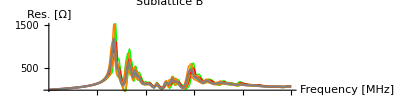

```mathematica
Show[meanSTDAbsDirectPlots,meanSTDAbsPlots[[2]]]
```

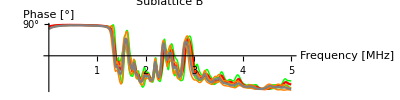

```mathematica
Show[meanSTDArgDirectPlots,meanSTDArgPlots[[2]]]
```

## Data Evaluation of backup Hand Measurements

```mathematica
(*Sorts imported data into the format: {j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataBackupOrdered = Table[backupImportdata[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[backupImportdata][[1]]},{entry,1,4}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOrderedBackup = Table[Transpose[{voltageDataBackupOrdered[[j,1,;;,1]]*1000,voltageDataBackupOrdered[[j,1,;;,2]],voltageDataBackupOrdered[[j,3,;;,2]]}],{j,1,Dimensions[backupImportdata][[1]]}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOrderedBackup = Table[Transpose[{voltageDataBackupOrdered[[j,1,;;,1]]*1000,voltageDataBackupOrdered[[j,2,;;,2]],voltageDataBackupOrdered[[j,4,;;,2]]}],{j,1,Dimensions[backupImportdata][[1]]}];

frequencyArrayBackup = voltage1JOrderedBackup[[1,;;,1]];

backupConfigNames = Table[FileNameTake[FileNames[backupDatapath<>"*"][[config]]],{config,1,Dimensions[backupImportdata][[1]]}];
```

```mathematica
subsystem = Dimensions[backupImportdata][[1]];

xMinMax =MinMax[correspondingNodeCoords[[;;subsystem,1]]];
yMinMax =MinMax[correspondingNodeCoords[[;;subsystem,2]]];

impedancesJOrderedBackup = Table[{frequencyArrayBackup[[freq]],(shuntR*(voltage2JOrderedBackup[[j,freq,2]])*Exp[I(voltage2JOrderedBackup[[j,freq,3]])*2 π/360])/(((voltage1JOrderedBackup[[j,freq,2]])*Exp[I(voltage1JOrderedBackup[[j,freq,3]])*2 π/360])-((voltage2JOrderedBackup[[j,freq,2]])*Exp[I(voltage2JOrderedBackup[[j,freq,3]])*2 π/360]))},{j,1,Dimensions[backupImportdata][[1]]},{freq,1,Length[frequencyArrayBackup]}];

ImpedancesArrayBackup = Table[impedancesJOrderedBackup[[Position[correspondingNodeCoords[[;;subsystem]],{x,y,sub}][[1,1]]]],{x,xMinMax[[1]],xMinMax[[2]]},{y,yMinMax[[1]],yMinMax[[2]]},{sub,1,2}];
```

```mathematica
Manipulate[ListLinePlot[{Abs[ImpedancesArrayBackup[[x,y,sub]]]},PlotRange->{All,All},AxesLabel->{"Frequency [Hz]","Res. [Ω]"},AspectRatio->1/4,ImageSize->Full,PlotLabel->"Impedance Spectrum of 'Repaired' Board 2"],{x,1,8,1},{y,1,8,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
absImpedanceBackupPlots =Table[ListLinePlot[Abs[ImpedancesArrayBackup[[x,y,sub]]],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,PlotStyle->Orange,AxesLabel->{"Frequency [Hz]","Res. [Ω]"},PlotLegends->{"Impedance spectrum of 'Repaired' Board 2"}],{x,xMinMax[[1]],xMinMax[[2]]},{y,yMinMax[[1]],yMinMax[[2]]},{sub,1,2}];

argImpedanceBackupPlots =Table[ListLinePlot[Transpose[{ImpedancesArrayBackup[[x,y,sub,;;,1]],Arg[ImpedancesArrayBackup[[x,y,sub,;;,2]]]}],PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotStyle->Orange,Ticks->{Automatic,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Phase [°]"},PlotLegends->{"Impedance spectrum of 'Repaired' Board 2"}],{x,xMinMax[[1]],xMinMax[[2]]},{y,yMinMax[[1]],yMinMax[[2]]},{sub,1,2}];
```

```mathematica
Manipulate[Show[absImpedancePlots[[x,y,sub]],absImpedanceBackupPlots[[x,y,sub]]],{x,1,8,1},{y,1,8,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
meanSTDAbsBackup = Table[Around[Mean[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]],StandardDeviation[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

meanSTDArgBackup = Table[Around[Mean[Arg[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]],StandardDeviation[Arg[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

meanAbsBackup = Table[Mean[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

meanArgBackup = Table[Mean[Arg[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

meanSTDAbsBackupPlots = Table[ListLinePlot[meanSTDAbsBackup[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->All,PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes 'Repaired' Board"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,ohmTicks},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];

meanSTDArgBackupPlots = Table[ListLinePlot[meanSTDArgBackup[[sub]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->All,PlotLegends->{"Average Phases over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes 'Repaired' Board"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks,degTicks},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2}];
```

```mathematica
backupSTD = Table[StandardDeviation[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,sub,i,2]]]]]/meanAbsBackup[[sub,i]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

backupSTDAdded = Table[(StandardDeviation[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,1,i,2]]]]]/meanAbsBackup[[1,i]])+(StandardDeviation[Abs[Flatten[ImpedancesArrayBackup[[;;,;;,2,i,2]]]]]/meanAbsBackup[[2,i]]),{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

STD = Table[StandardDeviation[Flatten[ImpedancesArray[[;;,;;,sub,i,2]]]]/meanAbs[[sub,i]],{sub,1,2},{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];

STDAdded =  Table[(StandardDeviation[Flatten[ImpedancesArray[[;;,;;,1,i,2]]]]/meanAbs[[1,i]])+(StandardDeviation[Abs[Flatten[ImpedancesArray[[;;,;;,2,i,2]]]]]/meanAbs[[2,i]]),{i,1,Length[ImpedancesArrayBackup[[1,1,1,;;,2]]]}];
```

```mathematica
addedMeans = meanAbs[[1,430;;470]]+meanAbs[[2,430;;470]];
addedMeansBackup = meanAbsBackup[[1,430;;470]]+meanAbsBackup[[2,430;;470]];

minAbsA = 430+Position[addedMeans,Min[addedMeans]][[1,1]]
minAbsBackupA =430+Position[addedMeansBackup,Min[addedMeansBackup]][[1,1]]
diff = minAbsA-minAbsBackupA;

STDAdded[[minAbsA]]
backupSTDAdded[[minAbsA]]
backupSTDAdded[[minAbsBackupA]]

frequencyArrayBackup[[(minAbsA)]]
frequencyArrayBackup[[(minAbsBackupA)]]
```

466

461

0.723294

0.588442

0.404806

2.38078096822391672×10^6

2.35625447544407507×10^6

```mathematica
meanSTDAbsBackupPlotsShifted23 = Table[ListLinePlot[meanSTDAbsBackup[[sub,400-diff;;600-diff]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->All,PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes 'Repaired' Board"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks23,ohmTicks23},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];
```

```mathematica
Manipulate[Show[meanSTDAbsBackupPlotsShifted23[[sub]],meanSTDAbsPlots23[[sub]]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
frequencyArray[[460]]
```

2.35134799959269003×10^6

```mathematica
minBackupSTDA =frequencyArrayBackup[[Position[backupSTD[[1]],Min[backupSTD[[1,400;;600]]]][[1,1]]]]
minBackupSTDB =frequencyArrayBackup[[Position[backupSTD[[2]],Min[backupSTD[[2,400;;600]]]][[1,1]]]]
minSTDA = frequencyArrayBackup[[Position[STD[[1]],Min[STD[[1,400;;600]]]][[1,1]]]]
minSTDB = frequencyArrayBackup[[Position[STD[[2]],Min[STD[[2,400;;600]]]][[1,1]]]]

minBackupSTDAdded =frequencyArrayBackup[[Position[backupSTDAdded,Min[backupSTDAdded[[400;;600]]]][[1,1]]]]
minSTDAdded =frequencyArrayBackup[[Position[STDAdded,Min[STDAdded[[400;;600]]]][[1,1]]]]
```

2.53282776770902274×10^6

2.57207201798337337×10^6

2.56226647570656542×10^6

2.15024942895070126×10^6

2.12082185089457243×10^6

2.14534325482418353×10^6

```mathematica
minBackupSTDAValley =frequencyArrayBackup[[Position[backupSTD[[1]],Min[backupSTD[[1,430;;470]]]][[1,1]]]]
minBackupSTDBValley =frequencyArrayBackup[[Position[backupSTD[[2]],Min[backupSTD[[2,430;;470]]]][[1,1]]]]
minSTDAValley = frequencyArrayBackup[[Position[STD[[1]],Min[STD[[1,430;;470]]]][[1,1]]]]
minSTDBValley = frequencyArrayBackup[[Position[STD[[2]],Min[STD[[2,430;;470]]]][[1,1]]]]

minBackupSTDAddedValley =frequencyArrayBackup[[Position[backupSTDAdded,Min[backupSTDAdded[[430;;470]]]][[1,1]]]]
minSTDAddedValley =frequencyArrayBackup[[Position[STDAdded,Min[STDAdded[[430;;470]]]][[1,1]]]]
```

2.24835074277507374×10^6

2.20420278674282599×10^6

2.31701853613230924×10^6

2.20420278674282599×10^6

2.35134799959269003×10^6

2.30230390411634289×10^6

```mathematica
frequencyArrayBackup[[430;;470]]
```

{2.20420278674282599×10^6,2.20910603707125119×10^6,2.21401771204909892×10^6,2.21892011882118822×10^6,2.22382209426541522×10^6,2.22873255211197829×10^6,2.23363368399986939×10^6,2.23853438478727185×10^6,2.2434397142205853×10^6,2.24835074277507374×10^6,2.25325236419848807×10^6,2.25816258762279176×10^6,2.26306336571724387×10^6,2.26796371248383366×10^6,2.27287271923160006×10^6,2.27778133307765529×10^6,2.28268042474155709×10^6,2.28758823413954815×10^6,2.29249517906282563×10^6,2.29739515202709299×10^6,2.30230390411634289×10^6,2.30720303397902217×10^6,2.31211098139283422×10^6,2.31701853613230924×10^6,2.32192569842482044×10^6,2.32682316141108458×10^6,2.3317295194829062×10^6,2.33663548488038987×10^6,2.34154105805828294×10^6,2.34645051841653185×10^6,2.35134799959269003×10^6,2.35625447544407507×10^6,2.36116055884849675×10^6,2.3660662498059537×10^6,2.3709715483164473×10^6,2.37587645437997708×10^6,2.38078096822391672×10^6,2.38568508962089254×10^6,2.39058881879827868×10^6,2.3954982636951172×10^6,2.4004032677567011×10^6}

```mathematica
Manipulate[meanSTDAbsBackupPlots[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[meanSTDArgBackupPlots[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[Show[meanSTDAbsBackupPlots[[sub]],meanSTDAbsPlots[[sub]]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
meanSTDAbsBackupPlots23 = Table[ListLinePlot[meanSTDAbsBackup[[sub,400;;600]],PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",PlotStyle->Red,IntervalMarkersStyle->Green,PlotRange->All,PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes 'Repaired' Board"},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,Ticks->{ticks23,ohmTicks23},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];
```

```mathematica
Manipulate[Show[meanSTDAbsBackupPlots23[[sub]],meanSTDAbsPlots23[[sub]]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
deviationOfNodesBackup = Table[Block[{peakSubABPos = {Position[meanAbsBackup,Max[meanAbsBackup[[1,If[freqs==1,400;;600,466]]]]][[1,2]], Position[meanAbsBackup,Max[meanAbsBackup[[1,If[freqs==1,400;;600,466]]]]][[1,2]]}},(Max[Abs[ImpedancesArrayBackup[[x,y,sub,peakSubABPos[[sub]],2]]]]-meanAbsBackup[[sub,peakSubABPos[[sub]]]])/(meanAbsBackup[[sub,peakSubABPos[[sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];

deviationHistBackup = Table[DiscretePlot3D[Abs[deviationOfNodesBackup[[freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHist,cellsHist,{{0,"0"},{0.3,"0.2"},{0.5,"0.4"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation in % from mean value of sublattice "<>ToString[If[sub==1,A,B]]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{sub,1,2}];
```

```mathematica
Manipulate[deviationHistBackup[[freqs,sub]],{freqs,1,2,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
oldMean23 = Max[meanAbs[[1,466]]]
newMean23 = Max[meanAbsBackup[[1,466]]]
```

46.0596

76.725

## Data Evaluation of old Hand Measurements

```mathematica
nodeCoordAndDataByHand=Transpose[{p1,byHandImportdata}];
sortedDataByHand=Partition[SortBy[nodeCoordAndDataByHand,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];

expAmplitudeByHandPlotReady=Table[sortedDataByHand[[sub;;All;;2,All,2,All,{1,2}]],{sub,1,2}];
expPhaseByHandPlotReady=Table[sortedDataByHand[[sub;;All;;2,All,2,All,{1,3}]],{sub,1,2}];

handOldFreqArray = expAmplitudeByHandPlotReady[[1,1,1,;;,1]];
```

```mathematica
singleHandComparisonAbsPlot =Table[ListLinePlot[{Transpose[{ImpedancesArray[[x,y,sub,;;,1]],Abs[ImpedancesArray[[x,y,sub,;;,2]]]}],Transpose[{handOldFreqArray,Abs[expAmplitudeByHandPlotReady[[sub,x,y,;;,2]]]}]},PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [kHz]","Res. [Ω]"},PlotLegends->{"Amplitude of impedance spectrum measured by Hand","Amplitude of old impedance spectrum measured by Hand"}],{x,1,4},{y,1,4},{sub,1,2}];

singleHandComparisonArgPlot =Table[ListLinePlot[{Transpose[{ImpedancesArray[[x,y,sub,;;,1]],Arg[ImpedancesArray[[x,y,sub,;;,2]]]}],Transpose[{handOldFreqArray,expPhaseByHandPlotReady[[sub,x,y,;;,2]]*2π/360}]},PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[y]<>","<>ToString[If[sub==1,"A","B"]]<>")",PlotRange->{Automatic,All},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [kHz]","Phase [°]"},Ticks->{ticks,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},PlotLegends->{"Phase of impedance spectrum measured by Hand","Phase of old impedance spectrum measured by Hand"}],{x,1,4},{y,1,4},{sub,1,2}];
```

```mathematica
Manipulate[singleHandComparisonAbsPlot[[x,y,sub]],{x,1,4,1},{y,1,4,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
Manipulate[singleHandComparisonArgPlot[[x,y,sub]],{x,1,4,1},{y,1,4,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
amplitudeHandAverage = Table[Mean[Flatten[expAmplitudeByHandPlotReady[[sub,;;,;;,i,2]]]],{sub,1,2},{i,1,Length[expAmplitudeByHandPlotReady[[1,1,1,;;,2]]]}];

amplitudeHandAverageSTD = Table[Around[Mean[Flatten[expAmplitudeByHandPlotReady[[sub,;;,;;,i,2]]]],StandardDeviation[Flatten[expAmplitudeByHandPlotReady[[sub,;;,;;,i,2]]]]],{sub,1,2},{i,1,Length[expAmplitudeByHandPlotReady[[1,1,1,;;,2]]]}];

phaseHandAverage = Table[Mean[Flatten[expPhaseByHandPlotReady[[sub,;;,;;,i,2]]]]*2π/360,{sub,1,2},{i,1,Length[expPhaseByHandPlotReady[[1,1,1,;;,2]]]}];

phaseHandAverageSTD = Table[Around[Mean[Flatten[expPhaseByHandPlotReady[[sub,;;,;;,i,2]]]]*2π/360,StandardDeviation[Flatten[expPhaseByHandPlotReady[[sub,;;,;;,i,2]]]]*2π/360],{sub,1,2},{i,1,Length[expPhaseByHandPlotReady[[1,1,1,;;,2]]]}];
```

```mathematica
maxHandToHand = Table[Max[meanAbs[[sub]]]/Max[amplitudeHandAverage[[sub,;;]]],{sub,1,2}];
ticks100 = Table[{i*1000000,i},{i,1,Length[ticks]}];

handComparisonAbsPlot = Table[ListLinePlot[{Transpose[{frequencyArray,(meanSTDAbs[[sub]])/(maxHandToHand[[sub]])}],Transpose[{handOldFreqArray,amplitudeHandAverageSTD[[sub]]}]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->{Orange,Green},PlotRange->{All,All},PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand (new), scaled by the factor "<>ToString[1/(maxHandToHand[[sub]])],"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand (old)"},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks100,{{500,"500"},{1000,"1000"}}},AxesLabel->{"Frequency [MHz]","Res. [Ω]"}],{sub,1,2}];

handComparisonArgPlot = Table[ListLinePlot[{Transpose[{frequencyArray,(meanSTDArg[[sub]])}],Transpose[{handOldFreqArray,phaseHandAverageSTD[[sub]]}]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->{Orange,Green},PlotRange->{All,All},PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand (new)","Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand (old)"},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks100,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2}];
```

```mathematica
Manipulate[handComparisonAbsPlot[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[handComparisonArgPlot[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

## Data Evaluation of Simulation

```mathematica
convertedData=Table[Block[{reIm = ToExpression[StringReplace[StringSplit[simulationImportdata[[node,i,j]],","],"e"->"*10^"]]},Abs[reIm[[1]]+I*reIm[[2]]]*Exp[I*Arg[reIm[[1]]+I*reIm[[2]]]]],{node,1,Dimensions[simulationImportdata][[1]]},{i,2,Dimensions[simulationImportdata][[2]]},{j,2,Dimensions[simulationImportdata][[3]]}];

impedanceData = Table[(convertedData[[node,i,1]])/(convertedData[[node,i,-1]]),{node,1,Dimensions[convertedData][[1]]},{i,2,Dimensions[convertedData][[2]]}];

freqData = Table[Block[{expr = ToExpression[simulationImportdata[[node,i,1]]]},expr],{node,1,Dimensions[simulationImportdata][[1]]},{i,2,Dimensions[simulationImportdata][[2]]}];
```

```mathematica
impedanceDataAbs=Table[{importdata[[2,i+1,1]],Abs[impedanceData[[node,i]]]},{node,1,Dimensions[impedanceData][[1]]},{i,1,Dimensions[impedanceData][[2]]}];

impedanceDataPhase = Table[{importdata[[2,i+1,1]],Arg[impedanceData[[node,i]]]},{node,1,Dimensions[impedanceData][[1]]},{i,1,Dimensions[impedanceData][[2]]}];
```

```mathematica
maxSimToMeas = Table[Max[meanAbs[[sub]]]/Max[impedanceDataAbs[[config,3;;,2]]],{sub,1,2},{config,1,Dimensions[simulationImportdata][[1]]}];
ticks10 = Table[{i*1000,i},{i,1,Length[ticks]}];
configNames = Table[FileNameTake[FileNames[simulationDatapath<>"*"][[config]]],{config,1,Dimensions[simulationImportdata][[1]]}];

comparisonAbsPlot = Table[ListLinePlot[{Transpose[{frequencyArray/1000,(meanSTDAbs[[sub]])/(maxSimToMeas[[sub,2*config+sub-2]])}][[;;997]],impedanceDataAbs[[2*config+sub-2,3;;]]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->Orange,PlotRange->{All,All},PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand, scaled by the factor "<>ToString[1/(maxSimToMeas[[sub,2*config+sub-2]])],"Amplitudes of Config: "<>ToString[configNames[[2*config+sub-2]]]},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks10,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}],{sub,1,2},{config,1,(Dimensions[simulationImportdata][[1]])/2}];

comparisonArgPlot = Table[ListLinePlot[{Transpose[{frequencyArray/1000,(meanSTDArg[[sub]])}][[;;997]],impedanceDataPhase[[2*config+sub-2,3;;]]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->Orange,PlotRange->{All,All},PlotLegends->{"Average Phases over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes by Hand","Phases of Config: "<>ToString[configNames[[2*config+sub-2]]]},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks10,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2},{config,1,(Dimensions[simulationImportdata][[1]])/2}];
```

```mathematica
Manipulate[comparisonAbsPlot[[sub,config]],{sub,1,2,1},{config,1,(Dimensions[simulationImportdata][[1]])/2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[comparisonArgPlot[[sub,config]],{sub,1,2,1},{config,1,4,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

## Data Evaluation of Multiplexer Measurements

```mathematica
nodeCoordAndDataWithMult=Transpose[{p1,multiplexerImportdata}];
sortedDataWithMult=Partition[SortBy[nodeCoordAndDataWithMult,#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],4];

expAmplitudeWithMultplexerPlotReady=Table[sortedDataWithMult[[sub;;All;;2,All,2,All,{1,2}]],{sub,1,2}];
expPhaseWithMultplexerPlotReady=Table[sortedDataWithMult[[sub;;All;;2,All,2,All,{1,3}]],{sub,1,2}];

multFreqArray = expAmplitudeWithMultplexerPlotReady[[1,1,1,;;,1]];
```

```mathematica
amplitudeMultiplexerAverage = Table[Mean[Flatten[expAmplitudeWithMultplexerPlotReady[[sub,;;,;;,i,2]]]],{sub,1,2},{i,1,Length[expAmplitudeWithMultplexerPlotReady[[1,1,1,;;,2]]]}];

amplitudeMultiplexerAverageSTD = Table[Around[Mean[Flatten[expAmplitudeWithMultplexerPlotReady[[sub,;;,;;,i,2]]]],StandardDeviation[Flatten[expAmplitudeWithMultplexerPlotReady[[sub,;;,;;,i,2]]]]],{sub,1,2},{i,1,Length[expAmplitudeWithMultplexerPlotReady[[1,1,1,;;,2]]]}];

phaseMultiplexerAverage = Table[Mean[Flatten[expPhaseWithMultplexerPlotReady[[sub,;;,;;,i,2]]]]*2π/360,{sub,1,2},{i,1,Length[expPhaseWithMultplexerPlotReady[[1,1,1,;;,2]]]}];

phaseMultiplexerAverageSTD = Table[Around[Mean[Flatten[expPhaseWithMultplexerPlotReady[[sub,;;,;;,i,2]]]]*2π/360,StandardDeviation[Flatten[expPhaseWithMultplexerPlotReady[[sub,;;,;;,i,2]]]]*2π/360],{sub,1,2},{i,1,Length[expPhaseWithMultplexerPlotReady[[1,1,1,;;,2]]]}];
```

```mathematica
maxHandToMult = Table[Max[meanAbs[[sub]]]/Max[amplitudeMultiplexerAverage[[sub,;;]]],{sub,1,2}];
ticks100 = Table[{i*1000000,i},{i,1,Length[ticks]}];

multComparisonAbsPlot = Table[ListLinePlot[{Transpose[{frequencyArray,(meanSTDAbs[[sub]])}],Transpose[{multFreqArray,amplitudeMultiplexerAverageSTD[[sub]]}]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->{Orange,Green},PlotRange->{All,All},PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes with BNC Board","Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes with Multiplexer"},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks100,{{1000,"1"},{2000,"2"},{3000,"3"},{4000,"4"},{5000,"5"},{6000,"6"},{7000,"7"},{8000,"8"}}},AxesLabel->{"Frequency [MHz]","Res. [kΩ]"}],{sub,1,2}];

multComparisonArgPlot = Table[ListLinePlot[{Transpose[{frequencyArray,(meanSTDArg[[sub]])}],Transpose[{multFreqArray,phaseMultiplexerAverageSTD[[sub]]}]},PlotLabel->"Sublattice "<>ToString[If[sub==1,"A","B"]],IntervalMarkers->"Bands",IntervalMarkersStyle->{Orange,Green},PlotRange->{All,All},PlotLegends->{"Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes with BNC Board","Average Amplitudes over all "<>ToString[If[sub==1,"A","B"]]<>" Nodes with Multiplexer"},PlotStyle->{Gray,Red},InterpolationOrder->3,ImageSize->Full,AspectRatio->1/4,Ticks->{ticks100,{{-π,"-180°"},{-π/2,"-90°"},{0,"0°"},{π/2,"90°"},{π,"180°"}}},AxesLabel->{"Frequency [MHz]","Phase [°]"}],{sub,1,2}];
```

```mathematica
Manipulate[multComparisonAbsPlot[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
Manipulate[multComparisonArgPlot[[sub]],{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

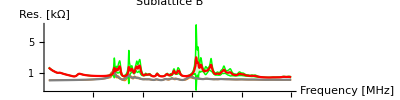

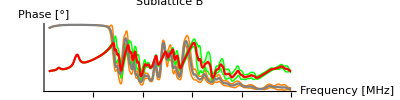

```mathematica
sub = 2;
multComparisonAbsPlot[[sub]]
multComparisonArgPlot[[sub]]
Clear[sub]
```